```mathematica
ClearAll;
Zeros[i_,j_]:= ConstantArray[0,{i,j}];
Eye[n_]:= IdentityMatrix[n];
Sat[x_,ϕ_]:= Piecewise[{{-1, x/ϕ≤  -1},{x/ϕ, x/ϕ > -1 && x/ϕ < 1},{1, x/ϕ≥  1}}];
```

```mathematica
n=2;
```

```mathematica
Subscript[NΩ, d]={1,2};
Subscript[NΩ, e]=Complement[Range[n],Subscript[NΩ, d]];
Subscript[NV, d]={};
Subscript[NV, e]=Complement[Range[2n],Subscript[NV, d]];
```

```mathematica
Subscript[𝓆, d]={Subscript[θ, 1][t],Subscript[θ, 2][t]};
Subscript[𝓆, e]={Subscript[x, 1][t],Subscript[y, 1][t],Subscript[x, 2][t],Subscript[y, 2][t]};
q=Join[Subscript[𝓆, d],Subscript[𝓆, e]];
```

```mathematica
Ωp ={Subscript[ω, z1][t],Subscript[ω, z2][t]};
Vp = {Subscript[v, x1][t],Subscript[v, y1][t],Subscript[v, x2][t],Subscript[v, y2][t]};
Subscript[𝓅, d]=Join[Ωp⟦Subscript[NΩ, d]⟧,Vp⟦Subscript[NV, d]⟧];
Subscript[𝓅, e]=Join[Ωp⟦Subscript[NΩ, e]⟧,Vp⟦Subscript[NV, e]⟧];
p=Join[Subscript[𝓅, d],Subscript[𝓅, e]];
```

```mathematica
p//MatrixForm
```

(ω_z1[t]
ω_z2[t]
v_x1[t]
v_y1[t]
v_x2[t]
v_y2[t])

```mathematica
m=Dimensions[Subscript[𝓅, e]]⟦1⟧;
```

```mathematica
Subscript[A, 1]={{Cos[Subscript[θ, 1][t]],-Sin[Subscript[θ, 1][t]],0},{Sin[Subscript[θ, 1][t]],Cos[Subscript[θ, 1][t]],0},{0,0,1}};
Subscript[A, 2]={{Cos[Subscript[θ, 2][t]],-Sin[Subscript[θ, 2][t]],Subscript[l, 1]},{Sin[Subscript[θ, 2][t]],Cos[Subscript[θ, 2][t]],0},{0,0,1}};
Subscript[col, 1]={Subscript[l, g1],0,1};
Subscript[col, 2]={Subscript[l, g2],0,1};
```

```mathematica
Subscript[H, 1]=Subscript[A, 1];
(Subscript[H, #+1]=FullSimplify@Dot[Subscript[H, #],Subscript[A, #+1]];)&/@Range[n-1];
```

```mathematica
(Subscript[R, #]=Subscript[H, #][[1;;2,1;;2]];)&/@Range[n];
```

```mathematica
(Subscript[S, #]=FullSimplify@Dot[Subscript[R, #] ᵀ,D[Subscript[R, #],t]];)&/@Range[n];
```

```mathematica
(Subscript[ω, #]=Subscript[S, #]⟦2,1⟧;)&/@Range[n];
```

```mathematica
(Subscript[X, #]=FullSimplify@Dot[Subscript[H, #],Subscript[col, #]];)&/@Range[n];
(Subscript[dX, #]=FullSimplify@D[Subscript[X, #]⟦1;;2⟧,t];)&/@Range[n];
```

```mathematica
(Subscript[v, #]=FullSimplify@Dot[Subscript[R, #] ᵀ,Subscript[dX, #]];)&/@Range[n];
(Subscript[𝔳, #]=FullSimplify@Dot[Subscript[R, #] ᵀ,D[Subscript[𝓆, e]⟦2 # -1;;2 #⟧, t]];)&/@Range[n];

V=Flatten[Subscript[v, #]&/@Range[n]];
𝔙=Flatten[Subscript[𝔳, #]&/@Range[n]];
Ω=Flatten[{Subscript[ω, #]}&/@Range[n]];

Subscript[𝒫, d]=Join[Ω⟦Subscript[NΩ, d]⟧,V⟦Subscript[NV, d]⟧];
Subscript[𝒫, e]=Join[Ω⟦Subscript[NΩ, e]⟧,V⟦Subscript[NV, e]⟧];
P = Join[Subscript[𝒫, d],Subscript[𝒫, e]];
RR = D[𝔙,{D[Subscript[𝓆, e], t]}]ᵀ;
```

```mathematica
P//MatrixForm
```

(θ_1'[t]
θ_1'[t]+θ_2'[t]
0
l_g1 θ_1'[t]
Sin[θ_2[t]] l_1 θ_1'[t]
(Cos[θ_2[t]] l_1+l_g2) θ_1'[t]+l_g2 θ_2'[t])

```mathematica
ψ=D[Subscript[𝒫, d],{D[Subscript[𝓆, d], t]}];
```

```mathematica
Υ=D[Subscript[𝒫, e],{D[Subscript[𝓆, d], t]}];
```

```mathematica
ℭ=Join[Eye[n],FullSimplify@Dot[Υ,Inverse[ψ]]];
dQ = Join[Dot[Inverse[ψ],Subscript[𝓅, d]],Dot[RR,Vp]];
Γ = D[dQ,{p}];
K=Join[FullSimplify@Dot[Υ,Inverse[ψ]],-Eye[m],2];
dK=Dot[Dot[D[K,{q}],Γ],p];
```

```mathematica
𝔖 =1/2∑_(i=1)^n ( Subscript[𝓂, i]((D[Vp⟦2i-1⟧, t])^2+(D[Vp⟦2i⟧, t])^2) + Subscript[Jz, i](D[Ωp⟦i⟧, t])^2);
Ep = ∑_(i=1)^n ( Subscript[𝓂, i] g Subscript[𝓆, e]⟦2i⟧);
```

```mathematica
G= FullSimplify@Dot[Γᵀ,D[Ep, {q}]];
f=D[𝔖, {D[p, t]}];
M=D[f, {D[p, t]}];
𝒱 = Simplify[f-Dot[M,D[p, t]]];
```

```mathematica
Sin2s={
Sin[Subscript[θ, 1][t]]-> Subscript[s, 1],
Cos[Subscript[θ, 1][t]] -> Subscript[c, 1],
Sin[Subscript[θ, 2][t]]-> Subscript[s, 2],
Cos[Subscript[θ, 2][t]] -> Subscript[c, 2],
Sin[Subscript[θ, 1][t]+Subscript[θ, 2][t]]-> Subscript[s, 12],
Cos[Subscript[θ, 1][t]+Subscript[θ, 2][t]]-> Subscript[c, 12]
};
```

```mathematica
ψ/.Sin2s//MatrixForm
```

(1 | 0
1 | 1)

```mathematica
ℭ/.Sin2s//MatrixForm
```

(1 | 0
0 | 1
0 | 0
l_g1 | 0
l_1 s_2 | 0
c_2 l_1 | l_g2)

```mathematica
K/.Sin2s//MatrixForm
```

(0 | 0 | -1 | 0 | 0 | 0
l_g1 | 0 | 0 | -1 | 0 | 0
l_1 s_2 | 0 | 0 | 0 | -1 | 0
c_2 l_1 | l_g2 | 0 | 0 | 0 | -1)

```mathematica
M/.Sin2s//MatrixForm
```

(Jz_1 | 0 | 0 | 0 | 0 | 0
0 | Jz_2 | 0 | 0 | 0 | 0
0 | 0 | 𝓂_1 | 0 | 0 | 0
0 | 0 | 0 | 𝓂_1 | 0 | 0
0 | 0 | 0 | 0 | 𝓂_2 | 0
0 | 0 | 0 | 0 | 0 | 𝓂_2)

```mathematica
𝒱/.Sin2s//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
G/.Sin2s//MatrixForm
```

(0
0
g s_1 𝓂_1
g c_1 𝓂_1
g s_12 𝓂_2
g c_12 𝓂_2)

```mathematica
SDATA ={
Subscript[l, 1]-> 1.0,
Subscript[l, 2] -> 1.0,
Subscript[l, g1] -> 0.5,
Subscript[l, g2] -> 0.5,
Subscript[𝓂, 1] -> 10.0,
Subscript[𝓂, 2] -> 10.0,
Subscript[Jz, 1] -> Subscript[𝓂, 1] Subscript[l, 1]^2/12,
Subscript[Jz, 2] -> Subscript[𝓂, 2] Subscript[l, 2]^2/12,
g-> 9.8
};
```

```mathematica
tf =4;
Δt = 0.01;
```

```mathematica
Subscript[q, dp][t_]:={2 π t, 2 π t};
RQ[t_]:= Inner[#1 -> #2 &,Subscript[𝓆, d],Subscript[q, dp][t],List];
ψn[t_]:=ψ//.SDATA/.RQ[t];
Cn[t_]:=ℭ//.SDATA/.RQ[t];
Mn[t_]:=M//.SDATA/.RQ[t];
Gn[t_]:=G//.SDATA/.RQ[t];
Subscript[p, dp][t_]:= Dot[ψn[t],Subscript[q, dp]'[t]];
Subscript[p, pp][t_]:= Dot[Cn[t],Subscript[p, dp][t]];
RP[t_]:= Inner[#1 -> #2&, p, Subscript[p, pp][t],List];
Vn[t_]:= 𝒱//.SDATA/.RQ[t]/.RP[t];
```

```mathematica
Fqn[t_]:= Dot[ψn[t]ᵀ,Dot[Cn[t]ᵀ,Dot[Mn[t], Subscript[p, pp]'[t]]+Vn[t]+Gn[t]]];
Fqn2=Fqn[Δt(#-1)]&/@Range[IntegerPart[tf/Δt]+1];
```

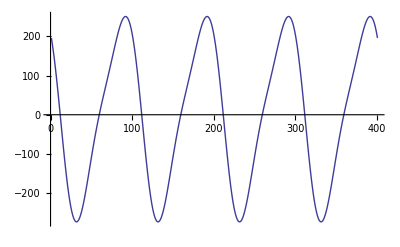

```mathematica
ListLinePlot[Fqn2⟦All,1⟧]
```

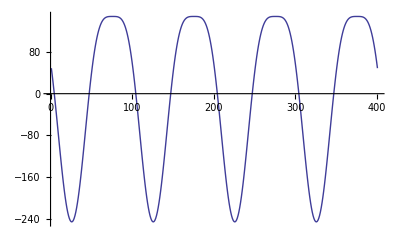

```mathematica
ListLinePlot[Fqn2⟦All,2⟧]
```

```mathematica
(* Acoplando 2 RRs *)
𝕟 = 2;
Subscript[𝕢, #]={Subscript[x, pp][t],Subscript[y, pp][t]};
Subscript[𝕢, 1]={Subscript[θ, 11][t],Subscript[θ, 12][t]};
Subscript[𝕢, 2]={Subscript[θ, 21][t],Subscript[θ, 22][t]};
Subscript[𝕢, o]=Join[Subscript[𝕢, 1],Subscript[𝕢, 2]];
𝕢𝕢 = Join[Subscript[𝕢, #],Subscript[𝕢, o]];
𝕟𝕢 = (Dimensions@𝕢𝕢)⟦1⟧;
Subscript[𝕡, #]={Subscript[dx, pp][t],Subscript[dy, pp][t]};
Subscript[𝕡, 1]={Subscript[ω, 11][t],Subscript[ω, 12][t]};
Subscript[𝕡, 2]={Subscript[ω, 21][t],Subscript[ω, 22][t]};
Subscript[𝕡, o]={Subscript[ω, 11][t],Subscript[ω, 12][t],Subscript[ω, 21][t],Subscript[ω, 22][t]};
𝕡𝕡 = Join[Subscript[𝕡, #],Subscript[𝕡, o]];
ℙ0 = {Subscript[dx, pp][t],Subscript[dy, pp][t]};
ℙ1 = {Subscript[ω, 11][t],Subscript[ω, 12][t],Subscript[v, x11][t],Subscript[v, y11][t],Subscript[v, x12][t],Subscript[v, y12][t]};
ℙ2 = {Subscript[ω, 21][t],Subscript[ω, 22][t],Subscript[v, x21][t],Subscript[v, y21][t],Subscript[v, x22][t],Subscript[v, y22][t]};
ℙ =Join[ℙ0,ℙ1,ℙ2];
𝕞 = (Dimensions@ℙ)⟦1⟧-𝕟;
ϕ = 
{Subscript[x, pp][t]-( -d/2+ Subscript[l, 1] Cos[Subscript[θ, 11][t]]+Subscript[l, 2] Cos[Subscript[θ, 11][t]+Subscript[θ, 12][t]]),
Subscript[y, pp][t]-( Subscript[l, 1] Sin[Subscript[θ, 11][t]]+Subscript[l, 2] Sin[Subscript[θ, 11][t]+Subscript[θ, 12][t]]),
Subscript[x, pp][t]-( d/2+ Subscript[l, 1] Cos[Subscript[θ, 21][t]]+Subscript[l, 2] Cos[Subscript[θ, 21][t]+Subscript[θ, 22][t]]),
Subscript[y, pp][t]-( Subscript[l, 1] Sin[Subscript[θ, 21][t]]+Subscript[l, 2] Sin[Subscript[θ, 21][t]+Subscript[θ, 22][t]])};
Λ = FullSimplify[Dot[D[ϕ, {Subscript[𝕢, #]}],Subscript[𝕡, #]]+Dot[Dot[D[ϕ, {Subscript[𝕢, 1]}],Inverse[ψ]],Subscript[𝕡, 1]]+Dot[Dot[D[ϕ, {Subscript[𝕢, 2]}],Inverse[ψ]],Subscript[𝕡, 2]]];
Subscript[𝕂, #]= FullSimplify[D[Λ, {Subscript[𝕡, #]}]];
Subscript[𝕂, o]= FullSimplify[D[Λ, {Subscript[𝕡, o]}]];Subscript[𝕂, #]//MatrixForm
```

(1 | 0
0 | 1
1 | 0
0 | 1)

```mathematica
Subscript[𝕂, o]//MatrixForm
```

(Sin[θ_11[t]] l_1 | Sin[θ_11[t]+θ_12[t]] l_2 | 0 | 0
-Cos[θ_11[t]] l_1 | -Cos[θ_11[t]+θ_12[t]] l_2 | 0 | 0
0 | 0 | Sin[θ_21[t]] l_1 | Sin[θ_21[t]+θ_22[t]] l_2
0 | 0 | -Cos[θ_21[t]] l_1 | -Cos[θ_21[t]+θ_22[t]] l_2)

```mathematica
ℂ =FullSimplify@Join[Eye[2],Dot[-Inverse[Subscript[𝕂, o]],Subscript[𝕂, #]]];ℂ//MatrixForm
```

(1 | 0
0 | 1
(Cos[θ_11[t]+θ_12[t]] Csc[θ_12[t]])/l_1 | (Csc[θ_12[t]] Sin[θ_11[t]+θ_12[t]])/l_1
-(Cos[θ_11[t]] Csc[θ_12[t]])/l_2 | -(Csc[θ_12[t]] Sin[θ_11[t]])/l_2
(Cos[θ_21[t]+θ_22[t]] Csc[θ_22[t]])/l_1 | (Csc[θ_22[t]] Sin[θ_21[t]+θ_22[t]])/l_1
-(Cos[θ_21[t]] Csc[θ_22[t]])/l_2 | -(Csc[θ_22[t]] Sin[θ_21[t]])/l_2)

```mathematica
FullSimplify@NullSpace[Join[Subscript[𝕂, #],Subscript[𝕂, o],2]]ᵀ//MatrixForm
```

(-Sin[θ_21[t]+θ_22[t]] l_2 | -Sin[θ_21[t]] l_1
Cos[θ_21[t]+θ_22[t]] l_2 | Cos[θ_21[t]] l_1
(Csc[θ_12[t]] Sin[θ_11[t]+θ_12[t]-θ_21[t]-θ_22[t]] l_2)/l_1 | Csc[θ_12[t]] Sin[θ_11[t]+θ_12[t]-θ_21[t]]
-Csc[θ_12[t]] Sin[θ_11[t]-θ_21[t]-θ_22[t]] | -(Csc[θ_12[t]] Sin[θ_11[t]-θ_21[t]] l_1)/l_2
0 | 1
1 | 0)

```mathematica
SUBS1 =
{Subscript[θ, 1][t]-> Subscript[θ, 11][t],
Subscript[θ, 2][t]-> Subscript[θ, 12][t]};
```

```mathematica
SUBS2 =
{Subscript[θ, 1][t]-> Subscript[θ, 21][t],
Subscript[θ, 2][t]-> Subscript[θ, 22][t]};
```

```mathematica
ℭ1 = ℭ/.SUBS1;ℭ1//MatrixForm
```

(1 | 0
0 | 1
0 | 0
l_g1 | 0
Sin[θ_12[t]] l_1 | 0
Cos[θ_12[t]] l_1 | l_g2)

```mathematica
ℭ2 = ℭ/.SUBS2;ℭ2//MatrixForm
```

(1 | 0
0 | 1
0 | 0
l_g1 | 0
Sin[θ_22[t]] l_1 | 0
Cos[θ_22[t]] l_1 | l_g2)

```mathematica
Join[Eye[2],Zeros[4,2]]  //MatrixForm
```

(1 | 0
0 | 1
0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
ℂℂ =FullSimplify@Dot[ℂᵀ,Join[Join[Eye[2],Zeros[4,2]],Join[Zeros[2,6],ℭ1ᵀ, Zeros[2,6]],Join[Zeros[4,6],ℭ2ᵀ],2]]ᵀ;ℂℂ//MatrixForm
```

(1 | 0
0 | 1
(Cos[θ_11[t]+θ_12[t]] Csc[θ_12[t]])/l_1 | (Csc[θ_12[t]] Sin[θ_11[t]+θ_12[t]])/l_1
-(Cos[θ_11[t]] Csc[θ_12[t]])/l_2 | -(Csc[θ_12[t]] Sin[θ_11[t]])/l_2
0 | 0
(Cos[θ_11[t]+θ_12[t]] Csc[θ_12[t]] l_g1)/l_1 | (Csc[θ_12[t]] Sin[θ_11[t]+θ_12[t]] l_g1)/l_1
Cos[θ_11[t]+θ_12[t]] | Sin[θ_11[t]+θ_12[t]]
Cos[θ_11[t]+θ_12[t]] Cot[θ_12[t]]-(Cos[θ_11[t]] Csc[θ_12[t]] l_g2)/l_2 | Cot[θ_12[t]] Sin[θ_11[t]+θ_12[t]]-(Csc[θ_12[t]] Sin[θ_11[t]] l_g2)/l_2
(Cos[θ_21[t]+θ_22[t]] Csc[θ_22[t]])/l_1 | (Csc[θ_22[t]] Sin[θ_21[t]+θ_22[t]])/l_1
-(Cos[θ_21[t]] Csc[θ_22[t]])/l_2 | -(Csc[θ_22[t]] Sin[θ_21[t]])/l_2
0 | 0
(Cos[θ_21[t]+θ_22[t]] Csc[θ_22[t]] l_g1)/l_1 | (Csc[θ_22[t]] Sin[θ_21[t]+θ_22[t]] l_g1)/l_1
Cos[θ_21[t]+θ_22[t]] | Sin[θ_21[t]+θ_22[t]]
Cos[θ_21[t]+θ_22[t]] Cot[θ_22[t]]-(Cos[θ_21[t]] Csc[θ_22[t]] l_g2)/l_2 | Cot[θ_22[t]] Sin[θ_21[t]+θ_22[t]]-(Csc[θ_22[t]] Sin[θ_21[t]] l_g2)/l_2)

```mathematica
d𝕢d𝕡 = Join[Join[Join[Eye[2],Zeros[4,2]],Join[Join[Zeros[2,2],Inverse[ψ]],Zeros[2,2]],2],Join[Zeros[4,2],Inverse[ψ]],2];d𝕢d𝕡 //MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | -1 | 1)

```mathematica
D[Λ, {ℙ}]//MatrixForm
```

(1 | 0 | Sin[θ_11[t]] l_1 | Sin[θ_11[t]+θ_12[t]] l_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -Cos[θ_11[t]] l_1 | -Cos[θ_11[t]+θ_12[t]] l_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ_21[t]] l_1 | Sin[θ_21[t]+θ_22[t]] l_2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -Cos[θ_21[t]] l_1 | -Cos[θ_21[t]+θ_22[t]] l_2 | 0 | 0 | 0 | 0)

```mathematica
K1 = K/.SUBS1;K1//MatrixForm
```

(0 | 0 | -1 | 0 | 0 | 0
l_g1 | 0 | 0 | -1 | 0 | 0
Sin[θ_12[t]] l_1 | 0 | 0 | 0 | -1 | 0
Cos[θ_12[t]] l_1 | l_g2 | 0 | 0 | 0 | -1)

```mathematica
K2 = K/.SUBS2;K2//MatrixForm
```

(0 | 0 | -1 | 0 | 0 | 0
l_g1 | 0 | 0 | -1 | 0 | 0
Sin[θ_22[t]] l_1 | 0 | 0 | 0 | -1 | 0
Cos[θ_22[t]] l_1 | l_g2 | 0 | 0 | 0 | -1)

```mathematica
Join[K1,Zeros[4,6]]//MatrixForm
```

(0 | 0 | -1 | 0 | 0 | 0
l_g1 | 0 | 0 | -1 | 0 | 0
Sin[θ_12[t]] l_1 | 0 | 0 | 0 | -1 | 0
Cos[θ_12[t]] l_1 | l_g2 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Join[Zeros[4,6],K2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
l_g1 | 0 | 0 | -1 | 0 | 0
Sin[θ_22[t]] l_1 | 0 | 0 | 0 | -1 | 0
Cos[θ_22[t]] l_1 | l_g2 | 0 | 0 | 0 | -1)

```mathematica
Join[Zeros[8,2],Join[K1,Zeros[4,6]],Join[Zeros[4,6],K2],2]//MatrixForm
```

(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | l_g1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Sin[θ_12[t]] l_1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[θ_12[t]] l_1 | l_g2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | l_g1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ_22[t]] l_1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[θ_22[t]] l_1 | l_g2 | 0 | 0 | 0 | -1)

```mathematica
D[Λ, {ℙ}]//MatrixForm
```

(1 | 0 | Sin[θ_11[t]] l_1 | Sin[θ_11[t]+θ_12[t]] l_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -Cos[θ_11[t]] l_1 | -Cos[θ_11[t]+θ_12[t]] l_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ_21[t]] l_1 | Sin[θ_21[t]+θ_22[t]] l_2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -Cos[θ_21[t]] l_1 | -Cos[θ_21[t]+θ_22[t]] l_2 | 0 | 0 | 0 | 0)

```mathematica
𝕂𝕂 =Join[Join[Zeros[8,2],Join[K1,Zeros[4,6]],Join[Zeros[4,6],K2],2],D[Λ, {ℙ}]];𝕂𝕂//MatrixForm
```

(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | l_g1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Sin[θ_12[t]] l_1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[θ_12[t]] l_1 | l_g2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | l_g1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ_22[t]] l_1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[θ_22[t]] l_1 | l_g2 | 0 | 0 | 0 | -1
1 | 0 | Sin[θ_11[t]] l_1 | Sin[θ_11[t]+θ_12[t]] l_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -Cos[θ_11[t]] l_1 | -Cos[θ_11[t]+θ_12[t]] l_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ_21[t]] l_1 | Sin[θ_21[t]+θ_22[t]] l_2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -Cos[θ_21[t]] l_1 | -Cos[θ_21[t]+θ_22[t]] l_2 | 0 | 0 | 0 | 0)

```mathematica
d𝕂𝕂 = FullSimplify@Dot[D[𝕂𝕂, {𝕢𝕢}], Dot[d𝕢d𝕡 ,𝕡𝕡]];d𝕂𝕂//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[θ_12[t]] l_1 (-ω_11[t]+ω_12[t]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Sin[θ_12[t]] l_1 (ω_11[t]-ω_12[t]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[θ_22[t]] l_1 (-ω_21[t]+ω_22[t]) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ_22[t]] l_1 (ω_21[t]-ω_22[t]) | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[θ_11[t]] l_1 ω_11[t] | Cos[θ_11[t]+θ_12[t]] l_2 ω_12[t] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Sin[θ_11[t]] l_1 ω_11[t] | Sin[θ_11[t]+θ_12[t]] l_2 ω_12[t] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[θ_21[t]] l_1 ω_21[t] | Cos[θ_21[t]+θ_22[t]] l_2 ω_22[t] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ_21[t]] l_1 ω_21[t] | Sin[θ_21[t]+θ_22[t]] l_2 ω_22[t] | 0 | 0 | 0 | 0)

```mathematica
FullSimplify@Dot[d𝕂𝕂,ℙ]//MatrixForm
```

(0
0
Cos[θ_12[t]] l_1 ω_11[t] (-ω_11[t]+ω_12[t])
Sin[θ_12[t]] l_1 ω_11[t] (ω_11[t]-ω_12[t])
0
0
Cos[θ_22[t]] l_1 ω_21[t] (-ω_21[t]+ω_22[t])
Sin[θ_22[t]] l_1 ω_21[t] (ω_21[t]-ω_22[t])
Cos[θ_11[t]] l_1 ω_11[t]^2+Cos[θ_11[t]+θ_12[t]] l_2 ω_12[t]^2
Sin[θ_11[t]] l_1 ω_11[t]^2+Sin[θ_11[t]+θ_12[t]] l_2 ω_12[t]^2
Cos[θ_21[t]] l_1 ω_21[t]^2+Cos[θ_21[t]+θ_22[t]] l_2 ω_22[t]^2
Sin[θ_21[t]] l_1 ω_21[t]^2+Sin[θ_21[t]+θ_22[t]] l_2 ω_22[t]^2)

```mathematica
FullSimplify@Dot[𝕂𝕂 ,ℂℂ]//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
M0 = {{Subscript[𝓂, pp],0},{0,Subscript[𝓂, pp]}};M0//MatrixForm
```

(𝓂_pp | 0
0 | 𝓂_pp)

```mathematica
M1 = M/.SUBS1; M1//MatrixForm
```

(Jz_1 | 0 | 0 | 0 | 0 | 0
0 | Jz_2 | 0 | 0 | 0 | 0
0 | 0 | 𝓂_1 | 0 | 0 | 0
0 | 0 | 0 | 𝓂_1 | 0 | 0
0 | 0 | 0 | 0 | 𝓂_2 | 0
0 | 0 | 0 | 0 | 0 | 𝓂_2)

```mathematica
M2 = M/.SUBS2; M2//MatrixForm
```

(Jz_1 | 0 | 0 | 0 | 0 | 0
0 | Jz_2 | 0 | 0 | 0 | 0
0 | 0 | 𝓂_1 | 0 | 0 | 0
0 | 0 | 0 | 𝓂_1 | 0 | 0
0 | 0 | 0 | 0 | 𝓂_2 | 0
0 | 0 | 0 | 0 | 0 | 𝓂_2)

```mathematica
𝕄𝕄dℙ = Join[Dot[M0,D[ℙ0, t]],Dot[M1,D[ℙ1, t]],Dot[M2,D[ℙ2, t]]];𝕄𝕄dℙ //MatrixForm
```

(𝓂_pp dx_pp'[t]
𝓂_pp dy_pp'[t]
Jz_1 ω_11'[t]
Jz_2 ω_12'[t]
𝓂_1 v_x11'[t]
𝓂_1 v_y11'[t]
𝓂_2 v_x12'[t]
𝓂_2 v_y12'[t]
Jz_1 ω_21'[t]
Jz_2 ω_22'[t]
𝓂_1 v_x21'[t]
𝓂_1 v_y21'[t]
𝓂_2 v_x22'[t]
𝓂_2 v_y22'[t])

```mathematica
𝕄𝕄 = D[𝕄𝕄dℙ, {D[ℙ, t]}];𝕄𝕄//MatrixForm
```

(𝓂_pp | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 𝓂_pp | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Jz_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Jz_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 𝓂_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 𝓂_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 𝓂_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 𝓂_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Jz_1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Jz_2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 𝓂_1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 𝓂_1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 𝓂_2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 𝓂_2)

```mathematica
G0 = {0,Subscript[𝓂, pp] g};G0//MatrixForm
```

(0
g 𝓂_pp)

```mathematica
G1 = G/.SUBS1; G1//MatrixForm
```

(0
0
g Sin[θ_11[t]] 𝓂_1
g Cos[θ_11[t]] 𝓂_1
g Sin[θ_11[t]+θ_12[t]] 𝓂_2
g Cos[θ_11[t]+θ_12[t]] 𝓂_2)

```mathematica
G2 = G/.SUBS2; G2//MatrixForm
```

(0
0
g Sin[θ_21[t]] 𝓂_1
g Cos[θ_21[t]] 𝓂_1
g Sin[θ_21[t]+θ_22[t]] 𝓂_2
g Cos[θ_21[t]+θ_22[t]] 𝓂_2)

```mathematica
𝔾𝔾 = Join[G0,G1,G2]; 𝔾𝔾//MatrixForm
```

(0
g 𝓂_pp
0
0
g Sin[θ_11[t]] 𝓂_1
g Cos[θ_11[t]] 𝓂_1
g Sin[θ_11[t]+θ_12[t]] 𝓂_2
g Cos[θ_11[t]+θ_12[t]] 𝓂_2
0
0
g Sin[θ_21[t]] 𝓂_1
g Cos[θ_21[t]] 𝓂_1
g Sin[θ_21[t]+θ_22[t]] 𝓂_2
g Cos[θ_21[t]+θ_22[t]] 𝓂_2)

```mathematica
𝔸 =FullSimplify@Join[Join[Eye[𝕟𝕢],Zeros[𝕟+𝕞,𝕟𝕢]],Join[Zeros[𝕟𝕢,𝕟+𝕞],Dot[ℂℂᵀ,𝕄𝕄],𝕂𝕂],2];𝔸//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 𝓂_pp | 0 | (Cos[θ_11[t]+θ_12[t]] Csc[θ_12[t]] Jz_1)/l_1 | -(Cos[θ_11[t]] Csc[θ_12[t]] Jz_2)/l_2 | 0 | (Cos[θ_11[t]+θ_12[t]] Csc[θ_12[t]] l_g1 𝓂_1)/l_1 | Cos[θ_11[t]+θ_12[t]] 𝓂_2 | (Cos[θ_11[t]+θ_12[t]] Cot[θ_12[t]]-(Cos[θ_11[t]] Csc[θ_12[t]] l_g2)/l_2) 𝓂_2 | (Cos[θ_21[t]+θ_22[t]] Csc[θ_22[t]] Jz_1)/l_1 | -(Cos[θ_21[t]] Csc[θ_22[t]] Jz_2)/l_2 | 0 | (Cos[θ_21[t]+θ_22[t]] Csc[θ_22[t]] l_g1 𝓂_1)/l_1 | Cos[θ_21[t]+θ_22[t]] 𝓂_2 | (Cos[θ_21[t]+θ_22[t]] Cot[θ_22[t]]-(Cos[θ_21[t]] Csc[θ_22[t]] l_g2)/l_2) 𝓂_2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 𝓂_pp | (Csc[θ_12[t]] Sin[θ_11[t]+θ_12[t]] Jz_1)/l_1 | -(Csc[θ_12[t]] Sin[θ_11[t]] Jz_2)/l_2 | 0 | (Csc[θ_12[t]] Sin[θ_11[t]+θ_12[t]] l_g1 𝓂_1)/l_1 | Sin[θ_11[t]+θ_12[t]] 𝓂_2 | (Cot[θ_12[t]] Sin[θ_11[t]+θ_12[t]]-(Csc[θ_12[t]] Sin[θ_11[t]] l_g2)/l_2) 𝓂_2 | (Csc[θ_22[t]] Sin[θ_21[t]+θ_22[t]] Jz_1)/l_1 | -(Csc[θ_22[t]] Sin[θ_21[t]] Jz_2)/l_2 | 0 | (Csc[θ_22[t]] Sin[θ_21[t]+θ_22[t]] l_g1 𝓂_1)/l_1 | Sin[θ_21[t]+θ_22[t]] 𝓂_2 | (Cot[θ_22[t]] Sin[θ_21[t]+θ_22[t]]-(Csc[θ_22[t]] Sin[θ_21[t]] l_g2)/l_2) 𝓂_2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | l_g1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ_12[t]] l_1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[θ_12[t]] l_1 | l_g2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | l_g1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ_22[t]] l_1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[θ_22[t]] l_1 | l_g2 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | Sin[θ_11[t]] l_1 | Sin[θ_11[t]+θ_12[t]] l_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -Cos[θ_11[t]] l_1 | -Cos[θ_11[t]+θ_12[t]] l_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ_21[t]] l_1 | Sin[θ_21[t]+θ_22[t]] l_2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -Cos[θ_21[t]] l_1 | -Cos[θ_21[t]+θ_22[t]] l_2 | 0 | 0 | 0 | 0)

```mathematica
F = {0,0,Subscript[τ, 1],0,0,0,0,0,Subscript[τ, 2],0,0,0,0,0};
```

```mathematica
𝔹 =Simplify@Join[Dot[d𝕢d𝕡,𝕡𝕡],Dot[ℂℂᵀ,F-𝔾𝔾],-Dot[d𝕂𝕂,ℙ]];
```

```mathematica
𝕏 = Join[D[𝕢𝕢, t],D[ℙ, t]];
```

```mathematica
Eq = Dot[𝔸,𝕏] == 𝔹;
```

```mathematica
(Subscript[eq, #]=Dot[𝔸,𝕏]⟦#⟧ == 𝔹⟦#⟧;)&/@Range[(Dimensions@𝔹)⟦1⟧];
```

```mathematica
Eq=Flatten[Subscript[eq, #]&/@Range[(Dimensions@𝔹)⟦1⟧]];
```

```mathematica
SDATA2 ={
Subscript[l, 1]-> 0.2,
Subscript[l, 2] -> 0.2,
Subscript[l, g1] -> 0.1,
Subscript[l, g2] -> 0.1,
Subscript[𝓂, 1] -> 0.054,
Subscript[𝓂, 2] -> 0.054,
Subscript[Jz, 1] -> Subscript[𝓂, 1] Subscript[l, 1]^2/12,
Subscript[Jz, 2] -> Subscript[𝓂, 2] Subscript[l, 2]^2/12,
g-> 9.8,
Subscript[𝓂, pp]-> 0.0
};
```

```mathematica
𝕏
```

{x_pp'[t],y_pp'[t],θ_11'[t],θ_12'[t],θ_21'[t],θ_22'[t],dx_pp'[t],dy_pp'[t],ω_11'[t],ω_12'[t],v_x11'[t],v_y11'[t],v_x12'[t],v_y12'[t],ω_21'[t],ω_22'[t],v_x21'[t],v_y21'[t],v_x22'[t],v_y22'[t]}

```mathematica
0.2Sin[72.0 π/180]+0.2Sin[144.0 π/180]
```

0.307768

```mathematica
CIq = {
Subscript[x, pp][0] == 0,
Subscript[y, pp][0] == (Subscript[l, 1] Sin[72.0 π/180]+Subscript[l, 2] Sin[144.0 π/180])/.SDATA2,
Subscript[θ, 11][0] == 72.0 π/180,
Subscript[θ, 12][0]== 72.0 π/180,
Subscript[θ, 21][0] == 108.0 π/180,
Subscript[θ, 22][0]== (108.0+180.0)π/180};
```

```mathematica
(Subscript[cip, #]=((ℙ⟦#⟧)/.t-> 0) == 0;)&/@Range[𝕟+𝕞];
```

```mathematica
CIp =Flatten[Subscript[cip, #]&/@Range[𝕟+𝕞]];
```

```mathematica
CIp//MatrixForm
```

(dx_pp[0]==0
dy_pp[0]==0
ω_11[0]==0
ω_12[0]==0
v_x11[0]==0
v_y11[0]==0
v_x12[0]==0
v_y12[0]==0
ω_21[0]==0
ω_22[0]==0
v_x21[0]==0
v_y21[0]==0
v_x22[0]==0
v_y22[0]==0)

```mathematica
CI = Join[CIq,CIp];CI//MatrixForm
```

(x_pp[0]==0
y_pp[0]==0.307768
θ_11[0]==1.25664
θ_12[0]==1.25664
θ_21[0]==1.88496
θ_22[0]==5.02655
dx_pp[0]==0
dy_pp[0]==0
ω_11[0]==0
ω_12[0]==0
v_x11[0]==0
v_y11[0]==0
v_x12[0]==0
v_y12[0]==0
ω_21[0]==0
ω_22[0]==0
v_x21[0]==0
v_y21[0]==0
v_x22[0]==0
v_y22[0]==0)

```mathematica
𝕗 = {Subscript[τ, 1],Subscript[τ, 2]};
```

```mathematica
ζ=D[Dot[ℂℂᵀ,F], {𝕗}];ζ// MatrixForm
```

((Cos[θ_11[t]+θ_12[t]] Csc[θ_12[t]])/l_1 | (Cos[θ_21[t]+θ_22[t]] Csc[θ_22[t]])/l_1
(Csc[θ_12[t]] Sin[θ_11[t]+θ_12[t]])/l_1 | (Csc[θ_22[t]] Sin[θ_21[t]+θ_22[t]])/l_1)

```mathematica
𝕄 = Dot[Inverse[ζ],ℂℂᵀ,𝕄𝕄,ℂℂ];
```

```mathematica
dℂℂ = FullSimplify@Dot[D[ℂℂ, {𝕢𝕢}], d𝕢d𝕡,𝕡𝕡];dℂℂ//MatrixForm
```

(0 | 0
0 | 0
(Csc[θ_12[t]]^2 (Cos[θ_12[t]] Cos[θ_11[t]+θ_12[t]] ω_11[t]-Cos[θ_11[t]] ω_12[t]))/l_1 | (Csc[θ_12[t]]^2 (Cos[θ_12[t]] Sin[θ_11[t]+θ_12[t]] ω_11[t]-Sin[θ_11[t]] ω_12[t]))/l_1
(Csc[θ_12[t]]^2 (-Cos[θ_11[t]+θ_12[t]] ω_11[t]+Cos[θ_11[t]] Cos[θ_12[t]] ω_12[t]))/l_2 | (Csc[θ_12[t]] (-Cos[θ_11[t]] ω_11[t]+Cot[θ_12[t]] Sin[θ_11[t]] (-ω_11[t]+ω_12[t])))/l_2
0 | 0
(Csc[θ_12[t]]^2 l_g1 (Cos[θ_12[t]] Cos[θ_11[t]+θ_12[t]] ω_11[t]-Cos[θ_11[t]] ω_12[t]))/l_1 | (Csc[θ_12[t]]^2 l_g1 (Cos[θ_12[t]] Sin[θ_11[t]+θ_12[t]] ω_11[t]-Sin[θ_11[t]] ω_12[t]))/l_1
-Sin[θ_11[t]+θ_12[t]] ω_12[t] | Cos[θ_11[t]+θ_12[t]] ω_12[t]
(Cos[θ_11[t]+θ_12[t]] Csc[θ_12[t]]^2 (l_2-l_g2) ω_11[t]-((Cos[θ_11[t]+θ_12[t]] Csc[θ_12[t]]^2+Cot[θ_12[t]] Sin[θ_11[t]+θ_12[t]]) l_2-Cos[θ_11[t]] Cot[θ_12[t]] Csc[θ_12[t]] l_g2) ω_12[t])/l_2 | (Csc[θ_12[t]]^2 Sin[θ_11[t]+θ_12[t]] (l_2-l_g2) ω_11[t]+((Cos[θ_11[t]+θ_12[t]] Cot[θ_12[t]]-Csc[θ_12[t]]^2 Sin[θ_11[t]+θ_12[t]]) l_2+Cot[θ_12[t]] Csc[θ_12[t]] Sin[θ_11[t]] l_g2) ω_12[t])/l_2
(Csc[θ_22[t]]^2 (Cos[θ_22[t]] Cos[θ_21[t]+θ_22[t]] ω_21[t]-Cos[θ_21[t]] ω_22[t]))/l_1 | (Csc[θ_22[t]]^2 (Cos[θ_22[t]] Sin[θ_21[t]+θ_22[t]] ω_21[t]-Sin[θ_21[t]] ω_22[t]))/l_1
(Csc[θ_22[t]]^2 (-Cos[θ_21[t]+θ_22[t]] ω_21[t]+Cos[θ_21[t]] Cos[θ_22[t]] ω_22[t]))/l_2 | (Csc[θ_22[t]] (-Cos[θ_21[t]] ω_21[t]+Cot[θ_22[t]] Sin[θ_21[t]] (-ω_21[t]+ω_22[t])))/l_2
0 | 0
(Csc[θ_22[t]]^2 l_g1 (Cos[θ_22[t]] Cos[θ_21[t]+θ_22[t]] ω_21[t]-Cos[θ_21[t]] ω_22[t]))/l_1 | (Csc[θ_22[t]]^2 l_g1 (Cos[θ_22[t]] Sin[θ_21[t]+θ_22[t]] ω_21[t]-Sin[θ_21[t]] ω_22[t]))/l_1
-Sin[θ_21[t]+θ_22[t]] ω_22[t] | Cos[θ_21[t]+θ_22[t]] ω_22[t]
(Cos[θ_21[t]+θ_22[t]] Csc[θ_22[t]]^2 (l_2-l_g2) ω_21[t]-((Cos[θ_21[t]+θ_22[t]] Csc[θ_22[t]]^2+Cot[θ_22[t]] Sin[θ_21[t]+θ_22[t]]) l_2-Cos[θ_21[t]] Cot[θ_22[t]] Csc[θ_22[t]] l_g2) ω_22[t])/l_2 | (Csc[θ_22[t]]^2 Sin[θ_21[t]+θ_22[t]] (l_2-l_g2) ω_21[t]+((Cos[θ_21[t]+θ_22[t]] Cot[θ_22[t]]-Csc[θ_22[t]]^2 Sin[θ_21[t]+θ_22[t]]) l_2+Cot[θ_22[t]] Csc[θ_22[t]] Sin[θ_21[t]] l_g2) ω_22[t])/l_2)

```mathematica
𝕍 = Dot[Inverse[ζ],ℂℂᵀ,𝕄𝕄,dℂℂ, Subscript[𝕡, #]];
```

```mathematica
𝔾 = Dot[Inverse[ζ],ℂℂᵀ,𝔾𝔾];
```

```mathematica
CONTROLDATA =
{Kp-> 100,
Kv-> 20,
λ->20,
k->0.1
};
```

```mathematica
r = {0.001Sin[2t],(Subscript[l, 1] Sin[72.0 π/180]+Subscript[l, 2] Sin[144.0 π/180])+0.001Sin[t]};
dr = D[r, t];
d2r = D[dr, t];
```

```mathematica
𝕗Control = 𝕍+𝔾+Dot[𝕄, d2r + Kv (dr - Subscript[𝕡, #])+ Kp(r-Subscript[𝕢, #])];
(*𝕗Control = 𝕍+𝔾+Dot[𝕄, d2r + λ(dr - Subscript[𝕡, #])+ k Sign[dr - Subscript[𝕡, #]+ λ(r-Subscript[𝕢, #])]];*)
(Subscript[subs𝕗Control, #]=𝕗⟦#⟧-> 𝕗Control⟦#⟧;)&/@Range[𝕟];
SUBS𝕗Control  =Flatten[Subscript[subs𝕗Control, #]&/@Range[𝕟]];
```

```mathematica
Sola =NDSolve[ Join[((Eq/.SUBS𝕗Control)//.SDATA2)/.CONTROLDATA,CI],Join[𝕢𝕢,ℙ],{t,0,20},MaxSteps->Infinity];
```

NDSolve::ndsdtc: The time constraint of 1. seconds was exceeded trying to solve for derivatives, so the system will be treated as a system of differential-algebraic equations. You can use Method->{"EquationSimplification"->"Solve"} to have the system solved as ordinary differential equations.

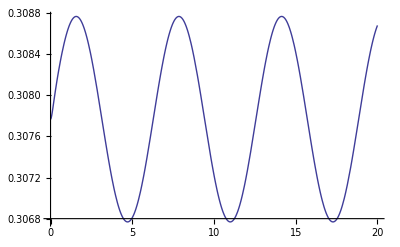

```mathematica
Plot[Evaluate[(Subscript[y, pp][t]/.Sola)],{t,0,20},PlotRange->All]
```

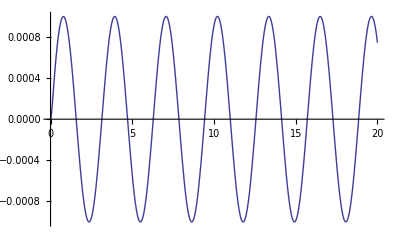

```mathematica
Plot[Evaluate[Subscript[x, pp][t]/.Sola],{t,0,20},PlotRange->All]
```

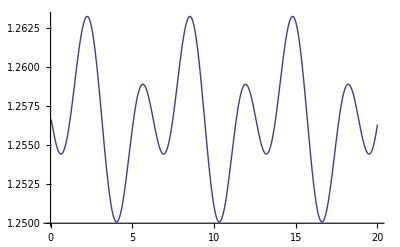

```mathematica
Plot[Evaluate[(Subscript[θ, 11][t]/.Sola)],{t,0,20},PlotRange->All]
```

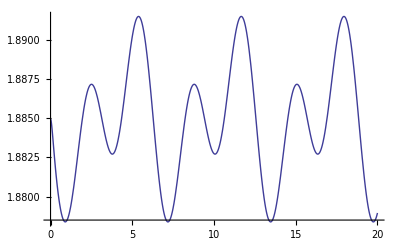

```mathematica
Plot[Evaluate[(Subscript[θ, 21][t]/.Sola)],{t,0,20},PlotRange->All]
```

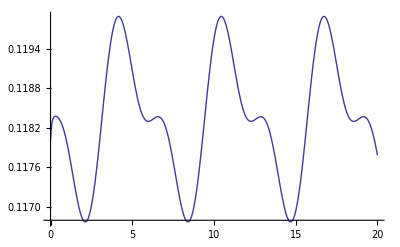

```mathematica
Plot[Evaluate[𝕗Control⟦1⟧//.SDATA2/.CONTROLDATA/.Sola],{t,0,20},PlotRange->All]
```

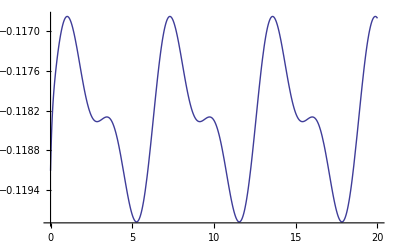

```mathematica
Plot[Evaluate[𝕗Control⟦2⟧//.SDATA2/.CONTROLDATA/.Sola],{t,0,20},PlotRange->All]
```